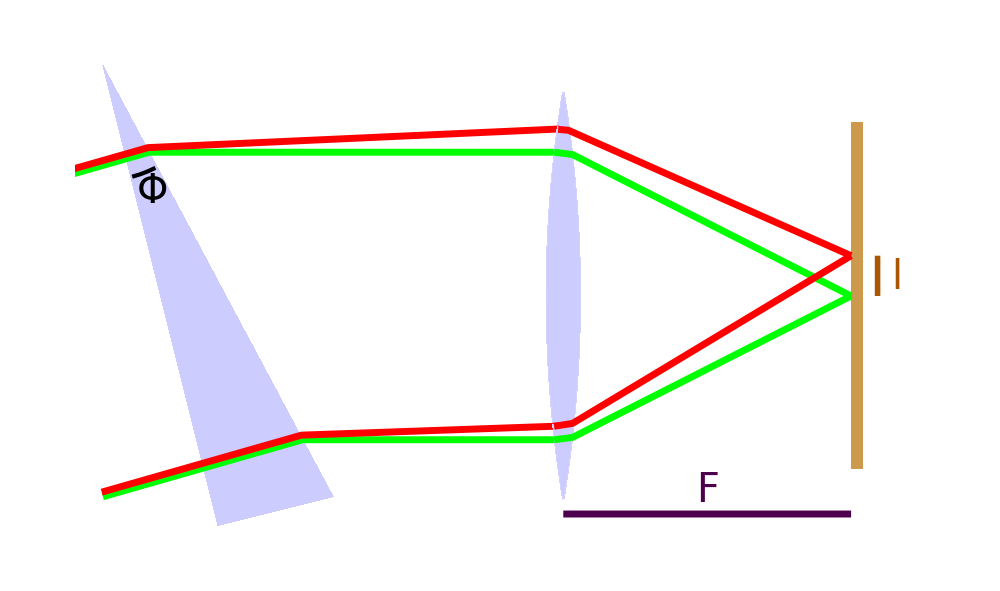

```mathematica
Show[Graphics[{RGBColor[0.8,0.8,1],Polygon[{{0,0},{1,0.25},{-1,4}}],Green,Thickness[0.005],Line[{{-1,1/4},{-1/8,1/2},{89/121,361/484},{3,361/484}}],Red,Line[{{-1-0.01,1/4+0.04},{-1/8-0.01,1/2+0.04},{89/121-0.01,361/484+0.04},{3,361/484+0.04+0.08}}],Green,Line[{{-1/8-2.5 8/15,1/2+2.5},{89/121-2.5 8/15,361/484+2.5},{3,361/484+2.5}}],Red,Line[{{-1/8-0.01-2.5 8/15,1/2+0.04+2.5},{89/121-0.01-2.5 8/15,361/484+0.04+2.5},{3,361/484+0.04+2.5+0.08 (2-(89/121-0.01-2.5 8/15))/(2-(89/121-0.01))}}],RGBColor[0.8,0.6,0.3],Rectangle[{5.5,0.5},{5.6,3.5}],Black,Thickness[0.003],Circle[{-1,4},1,{-1.313,-1.097}],Text[Style["Φ",Italic,40,FontFamily->"Times New Roman"],{-0.57,2.9}]},ImageSize->1000,PlotRange->{{-1.1,6},{-0.1,4.1}}],RegionPlot[(x-10.85-3)^2+(y-2)^2≤121&&(x+10.85-3)^2+(y-2)^2≤121,{x,-5,5},{y,-5,5},PlotPoints->200,BoundaryStyle->{White,Thickness[0]},Frame->False,PlotPoints->500,PlotStyle->RGBColor[0.8,0.8,1]],Graphics[{Green,Thickness[0.005],Line[{{2.92,361/484},{3.08,361/484+0.02},{5.5,361/484+1.25}}],Red,Line[{{2.955,361/484+0.04+2.5+0.08 (2-(89/121-0.01-2.5 8/15))/(2-(89/121-0.01))-0.005},{3.045,361/484+0.04+2.5+0.08 (2-(89/121-0.01-2.5 8/15))/(2-(89/121-0.01))-0.013},{5.5,361/484+1.6}}],Green,Line[{{2.92,361/484+2.5},{3.08,361/484+2.5-0.02},{5.5,361/484+1.25}}],Red,Line[{{2.92,361/484+0.04+0.08-0.003},{3.08,361/484+0.04+0.08+0.022},{5.5,361/484+1.6}}],RGBColor[0.3,0,0.3],Arrowheads[{-0.03,0.03}],Arrow[{{3,0.1},{5.5,0.1}}],Text[Style["F",Italic,40,FontFamily->"Times New Roman"],{4.25,0.3}],Darker[Orange],Arrowheads[{-0.02,0.02}],Thickness[0.004],Arrow[{{5.73,361/484+1.6},{5.73,361/484+1.25}}],Text[Style["l",Italic,40,FontFamily->"Times New Roman"],{5.9,361/484+1.41}]},ImageSize->1000,PlotRange->{{-1.1,5},{-0.1,4.1}}]]
```

```mathematica
Rasterize[-Graphics-,ImageResolution->200]
```

-Graphics-

```mathematica
361/484//N
```

0.745868

```mathematica
Solve[{(y-1/4)/(1/4)==(x+1)/(7/8),(x+1)/2==(y-4)/(-4+1/4)},{x,y}]
```

{{x→89/121,y→361/484}}

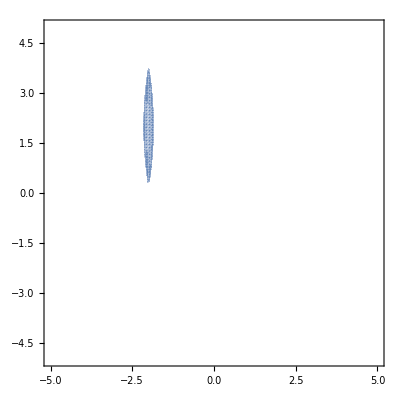

```mathematica
RegionPlot[(x-10.85+2)^2+(y-2)^2≤121&&(x+10.85+2)^2+(y-2)^2≤121,{x,-5,5},{y,-5,5},BoundaryStyle->{White,Thickness[0]},PlotPoints->100]
```

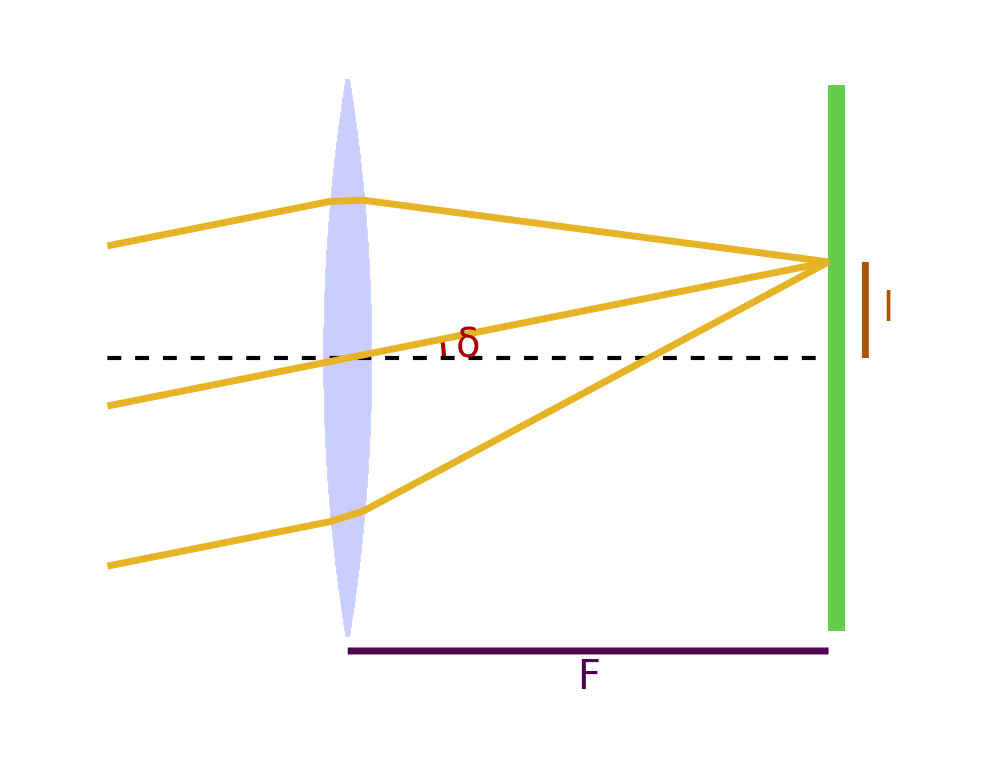

```mathematica
Show[Graphics[{RGBColor[0.4,0.8,0.3],Rectangle[{3,-1.7},{3.1,1.7}],Thickness[0.003],Darker[Red],Circle[{0,0},0.6,{0,0.2}]},ImageSize->1000,PlotRange->{{-1.6,3.5},{-2.1,1.8}}],RegionPlot[(x-10.85)^2+y^2≤121&&(x+10.85)^2+y^2≤121,{x,-5,5},{y,-5,5},PlotPoints->250,BoundaryStyle->{White,Thickness[0]},Frame->False,PlotPoints->750,PlotStyle->RGBColor[0.8,0.8,1]],Graphics[{Dashing[0.01],Thickness[0.003],Line[{{-1.5,0},{3,0}}]}],Graphics[{RGBColor[0.9,0.7,0.15],Thickness[0.005],Line[{{-1.5,-0.3},{0,0},{3,0.6}}],Line[{{-1.5,-0.3+1},{-0.11,1-0.11/5},{0.1,1-0.015},{3,0.6}}],Line[{{-1.5,-0.3-1},{-0.11,-1-0.11/5},{0.1,-1+0.045},{3,0.6}}],Darker[Red],Text[Style["δ",40,FontFamily->"Times New Roman"],{0.75,0.07}],Thickness[0.005],RGBColor[0.3,0,0.3],Arrowheads[{-0.03,0.03}],Arrow[{{0,-1.83},{3,-1.83}}],Text[Style["F",Italic,40,FontFamily->"Times New Roman"],{1.5,-2}],Darker[Orange],Arrow[{{3.23,0},{3.23,0.6}}],Text[Style["l",Italic,40,FontFamily->"Times New Roman"],{3.37,0.3}]}]]
```

```mathematica
(l √(1-n^2 Sin[ϕ]^2))/(F Sin[ϕ])/.l->0.1/.F->60/.n->1.5/.ϕ->8 Degree
```

0.0117116

```mathematica
l/(F Sin[ϕ])/.l->0.1/.F->60/.n->1.5/.ϕ->8 Degree
```

0.0119755

```mathematica
l/(F ϕ)/.l->0.1/.F->60/.n->1.5/.ϕ->8 Degree
```

0.0119366